Note: Acknowledgement: I got some help for these codes from Zain Salman Dar
#MATHEMATICAL MODELS OF SIGNAL-RESPONSE SYSTEMS

Q.no. 1:  Rate curves and signal-response curve for the ‘linear response case’

```mathematica
sys1 := {D[r[t],t]==k0 + k1 s -k2 r[t]}
```

```mathematica
prod1 := k0 + k1 s
```

```mathematica
deg1 := k2 r[t]
```

```mathematica
par1 = {k0->0.01, k1->1 , k2-> 5};
```

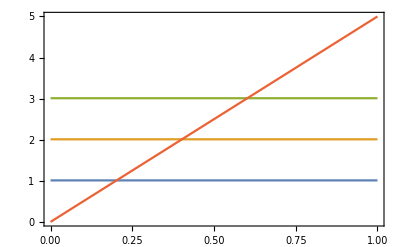

```mathematica
a1 = Plot[{(prod1 /. par1) /. s->1,(prod1 /. par1) /. s->2,(prod1 /. par1) /. s->3, deg1 /. par1},{r[t],0,1},Frame->True]
```

Next, I compute the intersection points between production terms and degradation terms (x-axis); substituting this value into either the production or degradation terms will yield the y-axis value.

```mathematica
solTemp1 = Solve[prod1 == deg1, r[t]]
```

{{r[t]→(k0+k1 s)/k2}}

```mathematica
tabTemp1 = {{r[t], prod1} /. solTemp1 /. par1 /. s->1,{r[t], prod1} /. solTemp1 /. par1 /. s->2,{r[t], prod1} /. solTemp1 /. par1 /. s->3}
```

{{{0.202,1.01}},{{0.402,2.01}},{{0.602,3.01}}}

```mathematica
a2 = ListPlot[tabTemp1,PlotStyle->{{Black,AbsolutePointSize[8]}}];
```

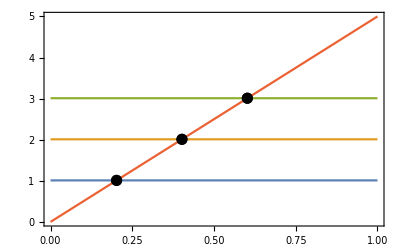

```mathematica
Show[a1,a2]
```

As discussed today in class, one can achieve this in a more automatized fashion by searching in the ODE system for the positive and negative terms:

```mathematica
List@@sys1[[1]][[2]]
```

{k0,k1 s,-k2 r[t]}

```mathematica
tmp1 = Cases[List@@sys1[[1]][[2]],n1_ /; If[Length[n1]>1,n1[[1]]==-1]]
```

{-k2 r[t]}

```mathematica
deg2 = - Plus@@tmp1
```

k2 r[t]

```mathematica
prod2 = Plus@@Complement[List@@sys1[[1]][[2]],tmp1]
```

k0+k1 s

```mathematica
Plot[{(prod2 /. par1) /. s->1,(prod2 /. par1) /. s->2,(prod2 /. par1) /. s->3, deg2 /. par1},{r[t],0,1},Frame->True]
```

-Graphics-

```mathematica
sys2 := {D[r[t],t]==k1 s (Rt-r[t])-k2 r[t]}
```

```mathematica
prod3 := k1 s Rt - k1 s r[t]
```

```mathematica
deg3 := k2 r[t]
```

```mathematica
part3 = {k1->1 , k2-> 1 , Rt -> 1};
a3= Plot[{(prod3 /. part3) /. s->2,(prod3 /. part3) /. s->4,(prod3 /. part3) /. s->8, deg3 /. part3},{r[t],0,1},Frame->True]
```

Q.no. 2: Rate curves and Signal-response curve for the ‘hyperbolic response case’

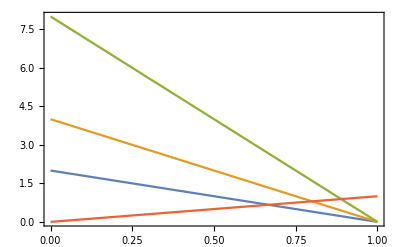

```mathematica
solTemp2 = Solve[prod3 == deg3, r[t]]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of d'[t]+d[t]==1+s.

Hold[solTemp2=Solve[prod3==deg3,r[t]]]

```mathematica
tabTemp2 = {{r[t], prod3} /. solTemp2 /. part3 /. s->2,{r[t], prod3} /. solTemp2 /. part3 /. s->4,{r[t], prod3} /. solTemp2 /. part3 /. s->8}
```

{{{2/3,2/3}},{{4/5,4/5}},{{8/9,8/9}}}

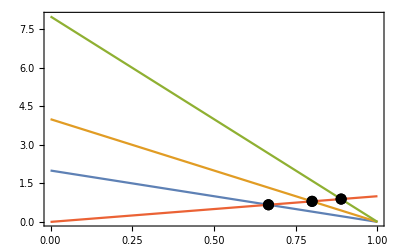

```mathematica
a4 = ListPlot[tabTemp2,PlotStyle->{{Black,AbsolutePointSize[8]}}];
Show[a3,a4]
```

```mathematica
sys3:= {D[r[t],t]==(k1 s(Rt-r[t]))/(km1+Rt-r[t]) - (k2r[t])/(km2+r[t])}
prod4 := (k1 s(Rt-r[t])(km2+r[t]))/((km1+Rt-r[t])(km2+r[t]))
```

```mathematica
deg4 := ((k2 r[t])(km1+Rt-r[t]))/((km1+Rt-r[t])(km2+r[t]))
```

```mathematica
part4 = {k1->1 , k2-> 1 , Rt -> 1, km1 -> 0.05, km2 -> 0.05};
```

```mathematica
a5= Plot[{(prod4 /. part4)/. s->0.25,(prod4 /. part4)/. s->0.5,(prod4 /. part4) /. s->1,(prod4 /. part4) /. s->1.5,(prod4 /. part4) /. s->2, deg4 /. part4},{r[t],0,1},Frame->True]
```

Q.no. 3: Rate curves and  signal-response curve for the ‘Sigmoidal response case’

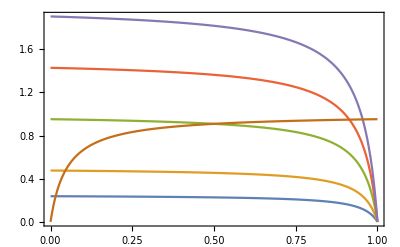

```mathematica
solTemp3 = Solve[prod4 == deg4, r[t]]
```

{{r[t]→(k2 km1+k2 Rt+k1 km2 s-k1 Rt s+√(-4 k1 km2 Rt s (k2-k1 s)+(-k2 km1-k2 Rt-k1 km2 s+k1 Rt s)^2))/(2 (k2-k1 s))},{r[t]→(-k2 km1-k2 Rt-k1 km2 s+k1 Rt s+√(-4 k1 km2 Rt s (k2-k1 s)+(-k2 km1-k2 Rt-k1 km2 s+k1 Rt s)^2))/(2 (-k2+k1 s))}}

```mathematica
tabTemp6 = {{r[t], prod4} /. solTemp3 /. part4 /. s->0.25,{r[t], prod4} /. solTemp3 /. part4 /. s->0.5,{r[t], prod4} /. solTemp3 /. part4 /. s->1, {r[t], prod4} /. solTemp3 /. part4 /. s->1.5, {r[t], prod4} /. solTemp3 /. part4 /. s->0.25, {r[t], prod4} /. solTemp3 /. part4 /. s->2}
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{{{1.06772,0.955266},{0.0156095,0.237916}},{{1.10474,0.9567},{0.0452595,0.475118}},{{ComplexInfinity,Indeterminate},{Indeterminate,Indeterminate}},{{-0.164096,1.43823},{0.914096,0.948138}},{{1.06772,0.955266},{0.0156095,0.237916}},{{-0.104741,1.9134},{0.954741,0.950236}}}

```mathematica
a6 = ListPlot[tabTemp6,PlotStyle->{{Black,AbsolutePointSize[8]}}];
```

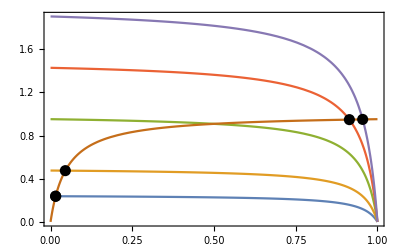

```mathematica
Show[a5,a6]
```

```mathematica
sys4:= {D[r[t],t] = k1 s - k2 x[t] r[t]}
```

```mathematica
prod6:= k3 s
prod5 := k1 s
deg6 := k4 x[t]
deg5 := k2  r[t]x[t]
part4 = {k1->2, k2-> 2 , k3 -> 1, k4 -> 1}
```

{k1→2,k2→2,k3→1,k4→1}

```mathematica
" a7= Plot[{(prod5 /. part4)/. s→1,(prod5 /. part4)/. s→2,(prod5/. part4) /. s→3,deg5 /. part4},{r[t],0,2},Frame→True]"
a19 = Plot[{(prod5 /. part4)/.s-> 1,(prod5 /. part4)/. s->2,(prod5/. part4) /.s->3,deg5 /. part4/.x[t] -> 2,deg5 /.part4 /. x[t] ->1, deg5 /. part4/. x[t] ->3},{r[t],0,2},Frame->True]
```

a7= Plot[{(prod5 /. part4)/. s→1,(prod5 /. part4)/. s→2,(prod5/. part4) /. s→3,deg5 /. part4},{r[t],0,2},Frame→True]

Q.no. 4: Rate curves and time course for the ‘adaptation device’

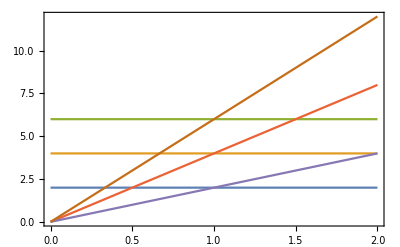

```mathematica
solTemp100 = Solve[prod5 == deg5, r[t]]
```

{{r[t]→(k1 s)/(k2 x[t])}}

```mathematica
tabTemp99 = {{r[t], prod5} /. solTemp100 /. part4 /. s->1/. x[t]->1,{r[t], prod5} /. solTemp100 /. part4 /. s->2/. x[t] -> 2,{r[t], prod5} /. solTemp100 /. part4 /. s->3 /.x[t] ->3}
```

{{{1,2}},{{1,4}},{{1,6}}}

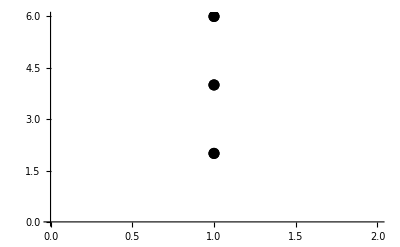

```mathematica
a89=ListPlot[tabTemp99,PlotStyle->{{Black,AbsolutePointSize[8]}}]
```

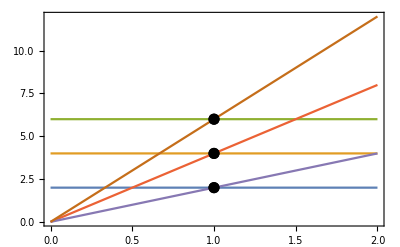

```mathematica
Show[a19,a89]
```

Q.no. 5: Rate curves and signal response curve for the ‘irreversible switch’

```mathematica
G[_u,_v,_j,_k]:= (2u k) / (v-u +v j +u k +(√((v - u +v j + u k)^2 - 4(v-u) u k)))
```

```mathematica
sys6:= {D[r[t],t] = k0 ((2 k3 r[t] j4)/(k4 - k3 r[t] + k4 j3 +k3 r[t] j4 +√((k4 - k3 r[t] + k4 j3 + k3 r[t] j4)^2 -4(k4 - k3 r[t]) k3 r[t] j4) ))+k1s -k2x r[t]}
```

```mathematica
prod7:= k0 ((2 k3 r[t] j4)/(k4 - k3 r[t] + k4 j3 +k3 r[t] j4 +√((k4 - k3 r[t] + k4 j3 + k3 r[t] j4)^2 -4(k4 - k3 r[t]) k3 r[t] j4) )) +k1 s
```

```mathematica
deg7 := k2 *r[t]*x[t]
```

```mathematica
part5 = {k0->0.4 , k1-> 0.01 , k2 -> 1, k3 -> 1, k4 -> 0.2, j3 -> 0.05, j4 -> 0.05 }
```

{k0→0.4,k1→0.01,k2→1,k3→1,k4→0.2,j3→0.05,j4→0.05}

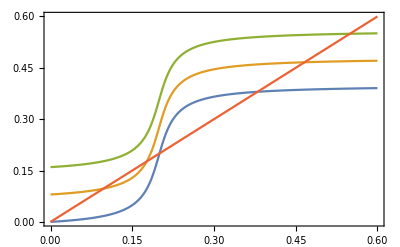

```mathematica
a8 = Plot[{(prod7 /. part5)/. s->0,(prod7 /. part5)/. s->8,(prod7/. part5) /. s->16, deg7 /. part5/.x[t]->1},{r[t],0,0.6},Frame->True]
```

```mathematica
solTemp9 = Reduce[Solve[prod7 == deg7, r[t]]]
```

Reduce::naqs: {r[t]→(k0 k3-j4 k0 k3+2 k1 k3 s+k2 k4 x[«1»])/(3 k2 k3 x[t])-(2^(1/3) (-Power[«2»] Power[«2»] Power[«2»]+3 Power[«2»] k3 Power[«2»] Plus[«7»]))/(3 k2^2 k3 x[t]^2 (Times[«5»]+Times[«6»]+«21»+Times[«4»]+Power[«2»])^(1/3))+(Times[«5»]+Times[«6»]+Times[«6»]+Times[«6»]+«18»+Times[«7»]+Times[«4»]+Power[«2»])^(1/3)/(3 2^(1/3) k2^2 k3 x[t]^2)}&&{«1»}&&{r[t]→(k0 k3-j4 k0 k3+2 k1 k3 s+k2 k4 x[«1»])/(3 k2 k3 x[t])+(«1»)/(«1»)-((«1») («1»)^(1/3))/(6 2^(«1») («2»)^2 k3 x[t]^2)} is not a quantified system of equations and inequalities.

Reduce[{{r[t]→(k0 k3-j4 k0 k3+2 k1 k3 s+k2 k4 x[t])/(3 k2 k3 x[t])-(2^(1/3) (-k2^2 x[t]^2 (k0 k3-j4 k0 k3+2 k1 k3 s+k2 k4 x[t])^2+3 k2^2 k3 x[t]^2 (-j4 k0^2 k3+k0 k1 k3 s-j4 k0 k1 k3 s+k1^2 k3 s^2+k0 k2 k4 x[t]+j3 k0 k2 k4 x[t]+2 k1 k2 k4 s x[t])))/(3 k2^2 k3 x[t]^2 (2 k0^3 k2^3 k3^3 x[t]^3+3 j4 k0^3 k2^3 k3^3 x[t]^3-3 j4^2 k0^3 k2^3 k3^3 x[t]^3-2 j4^3 k0^3 k2^3 k3^3 x[t]^3+3 k0^2 k1 k2^3 k3^3 s x[t]^3+12 j4 k0^2 k1 k2^3 k3^3 s x[t]^3+3 j4^2 k0^2 k1 k2^3 k3^3 s x[t]^3-3 k0 k1^2 k2^3 k3^3 s^2 x[t]^3+3 j4 k0 k1^2 k2^3 k3^3 s^2 x[t]^3-2 k1^3 k2^3 k3^3 s^3 x[t]^3-3 k0^2 k2^4 k3^2 k4 x[t]^4-9 j3 k0^2 k2^4 k3^2 k4 x[t]^4+6 j4 k0^2 k2^4 k3^2 k4 x[t]^4+9 j3 j4 k0^2 k2^4 k3^2 k4 x[t]^4+6 j4^2 k0^2 k2^4 k3^2 k4 x[t]^4+6 k0 k1 k2^4 k3^2 k4 s x[t]^4+9 j3 k0 k1 k2^4 k3^2 k4 s x[t]^4+3 j4 k0 k1 k2^4 k3^2 k4 s x[t]^4+6 k1^2 k2^4 k3^2 k4 s^2 x[t]^4-3 k0 k2^5 k3 k4^2 x[t]^5-9 j3 k0 k2^5 k3 k4^2 x[t]^5-6 j4 k0 k2^5 k3 k4^2 x[t]^5-6 k1 k2^5 k3 k4^2 s x[t]^5+2 k2^6 k4^3 x[t]^6+√((2 k0^3 k2^3 k3^3 x[t]^3+3 j4 k0^3 k2^3 k3^3 x[t]^3-3 j4^2 k0^3 k2^3 k3^3 x[t]^3-2 j4^3 k0^3 k2^3 k3^3 x[t]^3+3 k0^2 k1 k2^3 k3^3 s x[t]^3+12 j4 k0^2 k1 k2^3 k3^3 s x[t]^3+3 j4^2 k0^2 k1 k2^3 k3^3 s x[t]^3-3 k0 k1^2 k2^3 k3^3 s^2 x[t]^3+3 j4 k0 k1^2 k2^3 k3^3 s^2 x[t]^3-2 k1^3 k2^3 k3^3 s^3 x[t]^3-3 k0^2 k2^4 k3^2 k4 x[t]^4-9 j3 k0^2 k2^4 k3^2 k4 x[t]^4+6 j4 k0^2 k2^4 k3^2 k4 x[t]^4+9 j3 j4 k0^2 k2^4 k3^2 k4 x[t]^4+6 j4^2 k0^2 k2^4 k3^2 k4 x[t]^4+6 k0 k1 k2^4 k3^2 k4 s x[t]^4+9 j3 k0 k1 k2^4 k3^2 k4 s x[t]^4+3 j4 k0 k1 k2^4 k3^2 k4 s x[t]^4+6 k1^2 k2^4 k3^2 k4 s^2 x[t]^4-3 k0 k2^5 k3 k4^2 x[t]^5-9 j3 k0 k2^5 k3 k4^2 x[t]^5-6 j4 k0 k2^5 k3 k4^2 x[t]^5-6 k1 k2^5 k3 k4^2 s x[t]^5+2 k2^6 k4^3 x[t]^6)^2+4 (-k2^2 x[t]^2 (k0 k3-j4 k0 k3+2 k1 k3 s+k2 k4 x[t])^2+3 k2^2 k3 x[t]^2 (-j4 k0^2 k3+k0 k1 k3 s-j4 k0 k1 k3 s+k1^2 k3 s^2+k0 k2 k4 x[t]+j3 k0 k2 k4 x[t]+2 k1 k2 k4 s x[t]))^3))^(1/3))+1/(3 2^(1/3) k2^2 k3 x[t]^2)(2 k0^3 k2^3 k3^3 x[t]^3+3 j4 k0^3 k2^3 k3^3 x[t]^3-3 j4^2 k0^3 k2^3 k3^3 x[t]^3-2 j4^3 k0^3 k2^3 k3^3 x[t]^3+3 k0^2 k1 k2^3 k3^3 s x[t]^3+12 j4 k0^2 k1 k2^3 k3^3 s x[t]^3+3 j4^2 k0^2 k1 k2^3 k3^3 s x[t]^3-3 k0 k1^2 k2^3 k3^3 s^2 x[t]^3+3 j4 k0 k1^2 k2^3 k3^3 s^2 x[t]^3-2 k1^3 k2^3 k3^3 s^3 x[t]^3-3 k0^2 k2^4 k3^2 k4 x[t]^4-9 j3 k0^2 k2^4 k3^2 k4 x[t]^4+6 j4 k0^2 k2^4 k3^2 k4 x[t]^4+9 j3 j4 k0^2 k2^4 k3^2 k4 x[t]^4+6 j4^2 k0^2 k2^4 k3^2 k4 x[t]^4+6 k0 k1 k2^4 k3^2 k4 s x[t]^4+9 j3 k0 k1 k2^4 k3^2 k4 s x[t]^4+3 j4 k0 k1 k2^4 k3^2 k4 s x[t]^4+6 k1^2 k2^4 k3^2 k4 s^2 x[t]^4-3 k0 k2^5 k3 k4^2 x[t]^5-9 j3 k0 k2^5 k3 k4^2 x[t]^5-6 j4 k0 k2^5 k3 k4^2 x[t]^5-6 k1 k2^5 k3 k4^2 s x[t]^5+2 k2^6 k4^3 x[t]^6+√((2 k0^3 k2^3 k3^3 x[t]^3+3 j4 k0^3 k2^3 k3^3 x[t]^3-3 j4^2 k0^3 k2^3 k3^3 x[t]^3-2 j4^3 k0^3 k2^3 k3^3 x[t]^3+3 k0^2 k1 k2^3 k3^3 s x[t]^3+12 j4 k0^2 k1 k2^3 k3^3 s x[t]^3+3 j4^2 k0^2 k1 k2^3 k3^3 s x[t]^3-3 k0 k1^2 k2^3 k3^3 s^2 x[t]^3+3 j4 k0 k1^2 k2^3 k3^3 s^2 x[t]^3-2 k1^3 k2^3 k3^3 s^3 x[t]^3-3 k0^2 k2^4 k3^2 k4 x[t]^4-9 j3 k0^2 k2^4 k3^2 k4 x[t]^4+6 j4 k0^2 k2^4 k3^2 k4 x[t]^4+9 j3 j4 k0^2 k2^4 k3^2 k4 x[t]^4+6 j4^2 k0^2 k2^4 k3^2 k4 x[t]^4+6 k0 k1 k2^4 k3^2 k4 s x[t]^4+9 j3 k0 k1 k2^4 k3^2 k4 s x[t]^4+3 j4 k0 k1 k2^4 k3^2 k4 s x[t]^4+6 k1^2 k2^4 k3^2 k4 s^2 x[t]^4-3 k0 k2^5 k3 k4^2 x[t]^5-9 j3 k0 k2^5 k3 k4^2 x[t]^5-6 j4 k0 k2^5 k3 k4^2 x[t]^5-6 k1 k2^5 k3 k4^2 s x[t]^5+2 k2^6 k4^3 x[t]^6)^2+4 (-k2^2 x[t]^2 (k0 k3-j4 k0 k3+2 k1 k3 s+k2 k4 x[t])^2+3 k2^2 k3 x[t]^2 (-j4 k0^2 k3+k0 k1 k3 s-j4 k0 k1 k3 s+k1^2 k3 s^2+k0 k2 k4 x[t]+j3 k0 k2 k4 x[t]+2 k1 k2 k4 s x[t]))^3))^(1/3)},{r[t]→(k0 k3-j4 k0 k3+2 k1 k3 s+k2 k4 x[t])/(3 k2 k3 x[t])+((1+ⅈ √3) (-k2^2 x[t]^2 (k0 k3-j4 k0 k3+2 k1 k3 s+k2 k4 x[t])^2+3 k2^2 k3 x[t]^2 (-j4 k0^2 k3+k0 k1 k3 s-j4 k0 k1 k3 s+k1^2 k3 s^2+k0 k2 k4 x[t]+j3 k0 k2 k4 x[t]+2 k1 k2 k4 s x[t])))/(3 2^(2/3) k2^2 k3 x[t]^2 (2 k0^3 k2^3 k3^3 x[t]^3+3 j4 k0^3 k2^3 k3^3 x[t]^3-3 j4^2 k0^3 k2^3 k3^3 x[t]^3-2 j4^3 k0^3 k2^3 k3^3 x[t]^3+3 k0^2 k1 k2^3 k3^3 s x[t]^3+12 j4 k0^2 k1 k2^3 k3^3 s x[t]^3+3 j4^2 k0^2 k1 k2^3 k3^3 s x[t]^3-3 k0 k1^2 k2^3 k3^3 s^2 x[t]^3+3 j4 k0 k1^2 k2^3 k3^3 s^2 x[t]^3-2 k1^3 k2^3 k3^3 s^3 x[t]^3-3 k0^2 k2^4 k3^2 k4 x[t]^4-9 j3 k0^2 k2^4 k3^2 k4 x[t]^4+6 j4 k0^2 k2^4 k3^2 k4 x[t]^4+9 j3 j4 k0^2 k2^4 k3^2 k4 x[t]^4+6 j4^2 k0^2 k2^4 k3^2 k4 x[t]^4+6 k0 k1 k2^4 k3^2 k4 s x[t]^4+9 j3 k0 k1 k2^4 k3^2 k4 s x[t]^4+3 j4 k0 k1 k2^4 k3^2 k4 s x[t]^4+6 k1^2 k2^4 k3^2 k4 s^2 x[t]^4-3 k0 k2^5 k3 k4^2 x[t]^5-9 j3 k0 k2^5 k3 k4^2 x[t]^5-6 j4 k0 k2^5 k3 k4^2 x[t]^5-6 k1 k2^5 k3 k4^2 s x[t]^5+2 k2^6 k4^3 x[t]^6+√((2 k0^3 k2^3 k3^3 x[t]^3+3 j4 k0^3 k2^3 k3^3 x[t]^3-3 j4^2 k0^3 k2^3 k3^3 x[t]^3-2 j4^3 k0^3 k2^3 k3^3 x[t]^3+3 k0^2 k1 k2^3 k3^3 s x[t]^3+12 j4 k0^2 k1 k2^3 k3^3 s x[t]^3+3 j4^2 k0^2 k1 k2^3 k3^3 s x[t]^3-3 k0 k1^2 k2^3 k3^3 s^2 x[t]^3+3 j4 k0 k1^2 k2^3 k3^3 s^2 x[t]^3-2 k1^3 k2^3 k3^3 s^3 x[t]^3-3 k0^2 k2^4 k3^2 k4 x[t]^4-9 j3 k0^2 k2^4 k3^2 k4 x[t]^4+6 j4 k0^2 k2^4 k3^2 k4 x[t]^4+9 j3 j4 k0^2 k2^4 k3^2 k4 x[t]^4+6 j4^2 k0^2 k2^4 k3^2 k4 x[t]^4+6 k0 k1 k2^4 k3^2 k4 s x[t]^4+9 j3 k0 k1 k2^4 k3^2 k4 s x[t]^4+3 j4 k0 k1 k2^4 k3^2 k4 s x[t]^4+6 k1^2 k2^4 k3^2 k4 s^2 x[t]^4-3 k0 k2^5 k3 k4^2 x[t]^5-9 j3 k0 k2^5 k3 k4^2 x[t]^5-6 j4 k0 k2^5 k3 k4^2 x[t]^5-6 k1 k2^5 k3 k4^2 s x[t]^5+2 k2^6 k4^3 x[t]^6)^2+4 (-k2^2 x[t]^2 (k0 k3-j4 k0 k3+2 k1 k3 s+k2 k4 x[t])^2+3 k2^2 k3 x[t]^2 (-j4 k0^2 k3+k0 k1 k3 s-j4 k0 k1 k3 s+k1^2 k3 s^2+k0 k2 k4 x[t]+j3 k0 k2 k4 x[t]+2 k1 k2 k4 s x[t]))^3))^(1/3))-1/(6 2^(1/3) k2^2 k3 x[t]^2)(1-ⅈ √3) (2 k0^3 k2^3 k3^3 x[t]^3+3 j4 k0^3 k2^3 k3^3 x[t]^3-3 j4^2 k0^3 k2^3 k3^3 x[t]^3-2 j4^3 k0^3 k2^3 k3^3 x[t]^3+3 k0^2 k1 k2^3 k3^3 s x[t]^3+12 j4 k0^2 k1 k2^3 k3^3 s x[t]^3+3 j4^2 k0^2 k1 k2^3 k3^3 s x[t]^3-3 k0 k1^2 k2^3 k3^3 s^2 x[t]^3+3 j4 k0 k1^2 k2^3 k3^3 s^2 x[t]^3-2 k1^3 k2^3 k3^3 s^3 x[t]^3-3 k0^2 k2^4 k3^2 k4 x[t]^4-9 j3 k0^2 k2^4 k3^2 k4 x[t]^4+6 j4 k0^2 k2^4 k3^2 k4 x[t]^4+9 j3 j4 k0^2 k2^4 k3^2 k4 x[t]^4+6 j4^2 k0^2 k2^4 k3^2 k4 x[t]^4+6 k0 k1 k2^4 k3^2 k4 s x[t]^4+9 j3 k0 k1 k2^4 k3^2 k4 s x[t]^4+3 j4 k0 k1 k2^4 k3^2 k4 s x[t]^4+6 k1^2 k2^4 k3^2 k4 s^2 x[t]^4-3 k0 k2^5 k3 k4^2 x[t]^5-9 j3 k0 k2^5 k3 k4^2 x[t]^5-6 j4 k0 k2^5 k3 k4^2 x[t]^5-6 k1 k2^5 k3 k4^2 s x[t]^5+2 k2^6 k4^3 x[t]^6+√((2 k0^3 k2^3 k3^3 x[t]^3+3 j4 k0^3 k2^3 k3^3 x[t]^3-3 j4^2 k0^3 k2^3 k3^3 x[t]^3-2 j4^3 k0^3 k2^3 k3^3 x[t]^3+3 k0^2 k1 k2^3 k3^3 s x[t]^3+12 j4 k0^2 k1 k2^3 k3^3 s x[t]^3+3 j4^2 k0^2 k1 k2^3 k3^3 s x[t]^3-3 k0 k1^2 k2^3 k3^3 s^2 x[t]^3+3 j4 k0 k1^2 k2^3 k3^3 s^2 x[t]^3-2 k1^3 k2^3 k3^3 s^3 x[t]^3-3 k0^2 k2^4 k3^2 k4 x[t]^4-9 j3 k0^2 k2^4 k3^2 k4 x[t]^4+6 j4 k0^2 k2^4 k3^2 k4 x[t]^4+9 j3 j4 k0^2 k2^4 k3^2 k4 x[t]^4+6 j4^2 k0^2 k2^4 k3^2 k4 x[t]^4+6 k0 k1 k2^4 k3^2 k4 s x[t]^4+9 j3 k0 k1 k2^4 k3^2 k4 s x[t]^4+3 j4 k0 k1 k2^4 k3^2 k4 s x[t]^4+6 k1^2 k2^4 k3^2 k4 s^2 x[t]^4-3 k0 k2^5 k3 k4^2 x[t]^5-9 j3 k0 k2^5 k3 k4^2 x[t]^5-6 j4 k0 k2^5 k3 k4^2 x[t]^5-6 k1 k2^5 k3 k4^2 s x[t]^5+2 k2^6 k4^3 x[t]^6)^2+4 (-k2^2 x[t]^2 (k0 k3-j4 k0 k3+2 k1 k3 s+k2 k4 x[t])^2+3 k2^2 k3 x[t]^2 (-j4 k0^2 k3+k0 k1 k3 s-j4 k0 k1 k3 s+k1^2 k3 s^2+k0 k2 k4 x[t]+j3 k0 k2 k4 x[t]+2 k1 k2 k4 s x[t]))^3))^(1/3)},{r[t]→(k0 k3-j4 k0 k3+2 k1 k3 s+k2 k4 x[t])/(3 k2 k3 x[t])+((1-ⅈ √3) (-k2^2 x[t]^2 (k0 k3-j4 k0 k3+2 k1 k3 s+k2 k4 x[t])^2+3 k2^2 k3 x[t]^2 (-j4 k0^2 k3+k0 k1 k3 s-j4 k0 k1 k3 s+k1^2 k3 s^2+k0 k2 k4 x[t]+j3 k0 k2 k4 x[t]+2 k1 k2 k4 s x[t])))/(3 2^(2/3) k2^2 k3 x[t]^2 (2 k0^3 k2^3 k3^3 x[t]^3+3 j4 k0^3 k2^3 k3^3 x[t]^3-3 j4^2 k0^3 k2^3 k3^3 x[t]^3-2 j4^3 k0^3 k2^3 k3^3 x[t]^3+3 k0^2 k1 k2^3 k3^3 s x[t]^3+12 j4 k0^2 k1 k2^3 k3^3 s x[t]^3+3 j4^2 k0^2 k1 k2^3 k3^3 s x[t]^3-3 k0 k1^2 k2^3 k3^3 s^2 x[t]^3+3 j4 k0 k1^2 k2^3 k3^3 s^2 x[t]^3-2 k1^3 k2^3 k3^3 s^3 x[t]^3-3 k0^2 k2^4 k3^2 k4 x[t]^4-9 j3 k0^2 k2^4 k3^2 k4 x[t]^4+6 j4 k0^2 k2^4 k3^2 k4 x[t]^4+9 j3 j4 k0^2 k2^4 k3^2 k4 x[t]^4+6 j4^2 k0^2 k2^4 k3^2 k4 x[t]^4+6 k0 k1 k2^4 k3^2 k4 s x[t]^4+9 j3 k0 k1 k2^4 k3^2 k4 s x[t]^4+3 j4 k0 k1 k2^4 k3^2 k4 s x[t]^4+6 k1^2 k2^4 k3^2 k4 s^2 x[t]^4-3 k0 k2^5 k3 k4^2 x[t]^5-9 j3 k0 k2^5 k3 k4^2 x[t]^5-6 j4 k0 k2^5 k3 k4^2 x[t]^5-6 k1 k2^5 k3 k4^2 s x[t]^5+2 k2^6 k4^3 x[t]^6+√((2 k0^3 k2^3 k3^3 x[t]^3+3 j4 k0^3 k2^3 k3^3 x[t]^3-3 j4^2 k0^3 k2^3 k3^3 x[t]^3-2 j4^3 k0^3 k2^3 k3^3 x[t]^3+3 k0^2 k1 k2^3 k3^3 s x[t]^3+12 j4 k0^2 k1 k2^3 k3^3 s x[t]^3+3 j4^2 k0^2 k1 k2^3 k3^3 s x[t]^3-3 k0 k1^2 k2^3 k3^3 s^2 x[t]^3+3 j4 k0 k1^2 k2^3 k3^3 s^2 x[t]^3-2 k1^3 k2^3 k3^3 s^3 x[t]^3-3 k0^2 k2^4 k3^2 k4 x[t]^4-9 j3 k0^2 k2^4 k3^2 k4 x[t]^4+6 j4 k0^2 k2^4 k3^2 k4 x[t]^4+9 j3 j4 k0^2 k2^4 k3^2 k4 x[t]^4+6 j4^2 k0^2 k2^4 k3^2 k4 x[t]^4+6 k0 k1 k2^4 k3^2 k4 s x[t]^4+9 j3 k0 k1 k2^4 k3^2 k4 s x[t]^4+3 j4 k0 k1 k2^4 k3^2 k4 s x[t]^4+6 k1^2 k2^4 k3^2 k4 s^2 x[t]^4-3 k0 k2^5 k3 k4^2 x[t]^5-9 j3 k0 k2^5 k3 k4^2 x[t]^5-6 j4 k0 k2^5 k3 k4^2 x[t]^5-6 k1 k2^5 k3 k4^2 s x[t]^5+2 k2^6 k4^3 x[t]^6)^2+4 (-k2^2 x[t]^2 (k0 k3-j4 k0 k3+2 k1 k3 s+k2 k4 x[t])^2+3 k2^2 k3 x[t]^2 (-j4 k0^2 k3+k0 k1 k3 s-j4 k0 k1 k3 s+k1^2 k3 s^2+k0 k2 k4 x[t]+j3 k0 k2 k4 x[t]+2 k1 k2 k4 s x[t]))^3))^(1/3))-1/(6 2^(1/3) k2^2 k3 x[t]^2)(1+ⅈ √3) (2 k0^3 k2^3 k3^3 x[t]^3+3 j4 k0^3 k2^3 k3^3 x[t]^3-3 j4^2 k0^3 k2^3 k3^3 x[t]^3-2 j4^3 k0^3 k2^3 k3^3 x[t]^3+3 k0^2 k1 k2^3 k3^3 s x[t]^3+12 j4 k0^2 k1 k2^3 k3^3 s x[t]^3+3 j4^2 k0^2 k1 k2^3 k3^3 s x[t]^3-3 k0 k1^2 k2^3 k3^3 s^2 x[t]^3+3 j4 k0 k1^2 k2^3 k3^3 s^2 x[t]^3-2 k1^3 k2^3 k3^3 s^3 x[t]^3-3 k0^2 k2^4 k3^2 k4 x[t]^4-9 j3 k0^2 k2^4 k3^2 k4 x[t]^4+6 j4 k0^2 k2^4 k3^2 k4 x[t]^4+9 j3 j4 k0^2 k2^4 k3^2 k4 x[t]^4+6 j4^2 k0^2 k2^4 k3^2 k4 x[t]^4+6 k0 k1 k2^4 k3^2 k4 s x[t]^4+9 j3 k0 k1 k2^4 k3^2 k4 s x[t]^4+3 j4 k0 k1 k2^4 k3^2 k4 s x[t]^4+6 k1^2 k2^4 k3^2 k4 s^2 x[t]^4-3 k0 k2^5 k3 k4^2 x[t]^5-9 j3 k0 k2^5 k3 k4^2 x[t]^5-6 j4 k0 k2^5 k3 k4^2 x[t]^5-6 k1 k2^5 k3 k4^2 s x[t]^5+2 k2^6 k4^3 x[t]^6+√((2 k0^3 k2^3 k3^3 x[t]^3+3 j4 k0^3 k2^3 k3^3 x[t]^3-3 j4^2 k0^3 k2^3 k3^3 x[t]^3-2 j4^3 k0^3 k2^3 k3^3 x[t]^3+3 k0^2 k1 k2^3 k3^3 s x[t]^3+12 j4 k0^2 k1 k2^3 k3^3 s x[t]^3+3 j4^2 k0^2 k1 k2^3 k3^3 s x[t]^3-3 k0 k1^2 k2^3 k3^3 s^2 x[t]^3+3 j4 k0 k1^2 k2^3 k3^3 s^2 x[t]^3-2 k1^3 k2^3 k3^3 s^3 x[t]^3-3 k0^2 k2^4 k3^2 k4 x[t]^4-9 j3 k0^2 k2^4 k3^2 k4 x[t]^4+6 j4 k0^2 k2^4 k3^2 k4 x[t]^4+9 j3 j4 k0^2 k2^4 k3^2 k4 x[t]^4+6 j4^2 k0^2 k2^4 k3^2 k4 x[t]^4+6 k0 k1 k2^4 k3^2 k4 s x[t]^4+9 j3 k0 k1 k2^4 k3^2 k4 s x[t]^4+3 j4 k0 k1 k2^4 k3^2 k4 s x[t]^4+6 k1^2 k2^4 k3^2 k4 s^2 x[t]^4-3 k0 k2^5 k3 k4^2 x[t]^5-9 j3 k0 k2^5 k3 k4^2 x[t]^5-6 j4 k0 k2^5 k3 k4^2 x[t]^5-6 k1 k2^5 k3 k4^2 s x[t]^5+2 k2^6 k4^3 x[t]^6)^2+4 (-k2^2 x[t]^2 (k0 k3-j4 k0 k3+2 k1 k3 s+k2 k4 x[t])^2+3 k2^2 k3 x[t]^2 (-j4 k0^2 k3+k0 k1 k3 s-j4 k0 k1 k3 s+k1^2 k3 s^2+k0 k2 k4 x[t]+j3 k0 k2 k4 x[t]+2 k1 k2 k4 s x[t]))^3))^(1/3)}}]

```mathematica
tabTemp20 = {{r[t], prod7} /. solTemp9 /. part5 /. s->0/.x[t]-> 1,{r[t], prod7} /. solTemp9 /. part5 /. s->8/.x[t]-> 1,{r[t], prod7} /. solTemp19 /. part5 /. s->16/.x[t]->1}
```

ReplaceAll::reps: {Reduce[{{r[t]→1/3 Power[«2»] Power[«2»] Power[«2»] Plus[«4»]-1/3 Power[«2»] Power[«2»] Power[«2»] Power[«2»] Plus[«2»] Power[«2»]+1/3 Power[«2»] Power[«2»] Power[«2»] Power[«2»] Power[«2»]},{r[t]→«1»},{r[t]→1/3 Power[«2»] Power[«2»] Power[«2»] Plus[«4»]+1/3 Power[«2»] Plus[«2»] Power[«2»] Power[«2»] Power[«2»] Plus[«2»] Power[«2»]-1/6 Power[«2»] Plus[«2»] Power[«2»] Power[«2»] Power[«2»] Power[«2»]}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Reduce::naqs: {r[t]→(0.38+0.02 s+0.2 x[«1»])/(3 x[t])-(2^(1/3) (-Power[«2»] Power[«2»]+3 Power[«2»] Plus[«5»]))/(3 x[t]^2 (Times[«2»]+Times[«3»]+Times[«3»]+«6»+Times[«2»]+Power[«2»])^(1/3))+(Times[«2»]+Times[«3»]+Times[«3»]+Times[«3»]+«4»+Times[«3»]+Times[«2»]+Power[«2»])^(1/3)/(3 2^(1/3) x[t]^2)}&&{r[t]→«1»}&&{r[t]→(0.38+0.02 s+0.2 x[«1»])/(3 x[t])+((1-ⅈ Power[«2»]) (-«1» «1»+«1»))/(3 2^(2/3) («1»)^2 («1»+«9»+«1»)^(1/3))-((1+ⅈ Power[«2»]) («1»)^(1/3))/(6 2^(1/3) x[t]^2)} is not a quantified system of equations and inequalities.

ReplaceAll::reps: {Reduce[{{r[t]→1/3 Plus[«3»] Power[«2»]-1/3 Power[«2»] Power[«2»] Plus[«2»] Power[«2»]+1/3 Power[«2»] Power[«2»] Power[«2»]},{r[t]→1/3 Plus[«3»] Power[«2»]+1/3 Power[«2»] Plus[«2»] Power[«2»] Plus[«2»] Power[«2»]-1/6 Power[«2»] Plus[«2»] Power[«2»] Power[«2»]},{r[t]→1/3 Plus[«3»] Power[«2»]+1/3 Power[«2»] Plus[«2»] Power[«2»] Plus[«2»] Power[«2»]-1/6 Power[«2»] Plus[«2»] Power[«2»] Power[«2»]}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Reduce::naqs: {r[t]→(0.38+0.2 x[«1»])/(3 x[t])-(2^(1/3) (3 Plus[«2»] Power[«2»]-Power[«2»] Power[«2»]))/(3 x[t]^2 (0.+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Power[«2»])^(1/3))+(0.+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Power[«2»])^(1/3)/(3 2^(1/3) x[t]^2)}&&{r[t]→(0.38+0.2 «1»)/(3 x[t])+«1»-((«1») «1»)/(6 «1» «1»)}&&{r[t]→(0.38+0.2 x[«1»])/(3 x[t])+((1-ⅈ Power[«2»]) («1»))/(3 2^(2/3) x[t]^2 («1»)^(1/3))-((1+ⅈ Power[«2»]) (0.+«4»+Power[«2»])^(1/3))/(6 2^(1/3) x[t]^2)} is not a quantified system of equations and inequalities.

ReplaceAll::reps: {Reduce[{{r[t]→1/3 Plus[«2»] Power[«2»]-1/3 Power[«2»] Power[«2»] Plus[«2»] Power[«2»]+1/3 Power[«2»] Power[«2»] Power[«2»]},{r[t]→1/3 Plus[«2»] Power[«2»]+1/3 Power[«2»] Plus[«2»] Power[«2»] Plus[«2»] Power[«2»]-1/6 Power[«2»] Plus[«2»] Power[«2»] Power[«2»]},{r[t]→1/3 Plus[«2»] Power[«2»]+1/3 Power[«2»] Plus[«2»] Power[«2»] Plus[«2»] Power[«2»]-1/6 Power[«2»] Plus[«2»] Power[«2»] Power[«2»]}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Reduce::naqs: {r[t]→0.38+1.38778×10^-17 ⅈ}&&{r[t]→-2.77556×10^-17+6.93889×10^-18 ⅈ}&&{r[t]→0.2-1.38778×10^-17 ⅈ} is not a quantified system of equations and inequalities.

General::stop: Further output of Reduce::naqs will be suppressed during this calculation.

{{r[t],0.+(0.04 r[t])/(0.21-0.95 r[t]+√((0.21-0.95 r[t])^2-0.2 (0.2-r[t]) r[t]))}/.Reduce[{{r[t]→0.38+1.38778×10^-17 ⅈ},{r[t]→-2.77556×10^-17+6.93889×10^-18 ⅈ},{r[t]→0.2-1.38778×10^-17 ⅈ}}],{r[t],0.08+(0.04 r[t])/(0.21-0.95 r[t]+√((0.21-0.95 r[t])^2-0.2 (0.2-r[t]) r[t]))}/.Reduce[{{r[t]→0.466224+6.93889×10^-18 ⅈ},{r[t]→0.0971492-1.38778×10^-17 ⅈ},{r[t]→0.176626+1.38778×10^-17 ⅈ}}],{r[t],0.16+(0.04 r[t])/(0.21-0.95 r[t]+√((0.21-0.95 r[t])^2-0.2 (0.2-r[t]) r[t]))}/.solTemp19}

```mathematica
a16 = ListPlot[tabTemp20,PlotStyle->{{Black,AbsolutePointSize[8]}}];
```

ReplaceAll::reps: {Reduce[{{r[t]→0.38+1.38778×10^-17 ⅈ},{r[t]→-2.77556×10^-17+6.93889×10^-18 ⅈ},{r[t]→0.2-1.38778×10^-17 ⅈ}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Reduce[{{r[t]→0.466224+6.93889×10^-18 ⅈ},{r[t]→0.0971492-1.38778×10^-17 ⅈ},{r[t]→0.176626+1.38778×10^-17 ⅈ}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {solTemp19} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
Show[a8,a16]
```

-Graphics-

```mathematica
prod8 := k0 +k1 s
```

```mathematica
deg8 :=  k2 *r[t] +k22* ((2 *k3 * j4)/(k4 *r[t]- k3  + k4 *r[t]*j3 +k3* j4 +√((k4* r[t] - k3  + k4* r[t]* j3 + k3*  j4)^2 -4(k4 *r[t] - k3) k3 *j4) ))*r[t]
```

```mathematica
part6 = {k0->0, k1-> 0.05 , k2 -> 0.1, k22 -> 0.5, k3 -> 1,k4 -> 0.2, j3 -> 0.05, j4 -> 0.05 }
```

{k0→0,k1→0.05,k2→0.1,k22→0.5,k3→1,k4→0.2,j3→0.05,j4→0.05}

{k0→0,k1→0.05,k2→0.1,k22→0.5,k3→1,k4→0.2,j3→0.05,j4→0.05}

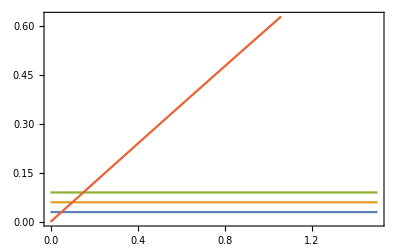

```mathematica
a9 = Plot[{(prod8 /. part6)/. s->0.6,(prod8 /. part6)/. s->1.2,(prod8/. part6) /. s->1.8, deg8 /. part6},{r[t],0,1.5},Frame->True]
```

Q.no. 6: Rate curves and the signal response curve for the ‘homeostatic response’

```mathematica
prod9 := k2 s r[t]
```

```mathematica
deg9 := k0 ((2 k3  j4)/(k4 r[t]- k3  + k4 r[t]j3 +k3  j4 +√((k4 r[t] - k3  + k4 r[t] j3 + k3  j4)^2 -4(k4 r[t] - k3) k3 j4) ))
```

```mathematica
part7 = {k0->1, k2 -> 1,k3 -> 0.5,k4 -> 1, j3 -> 0.01, j4 -> 0.01 }
```

{k0→1,k2→1,k3→0.5,k4→1,j3→0.01,j4→0.01}

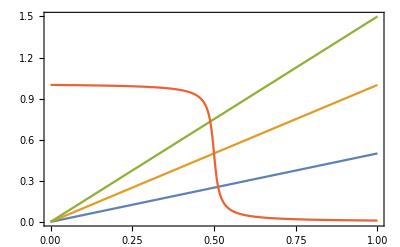

```mathematica
a9 = Plot[{(prod9/. part7)/. s->0.5,(prod9 /. part7)/. s->1,(prod9/. part7) /. s->1.5, deg9 /. part7},{r[t],0,1},Frame->True]
```

```mathematica
solTemp4 = Solve[prod9 == deg9, r[t]]
```

{{r[t]→(k0 k4+j3 k0 k4+k2 k3 s)/(3 k2 k4 s)-(2^(1/3) (-3 (-1+j4) k0 k2^3 k3 k4 s^3-k2^2 s^2 (k0 k4+j3 k0 k4+k2 k3 s)^2))/(3 k2^2 k4 s^2 (2 k0^3 k2^3 k4^3 s^3+6 j3 k0^3 k2^3 k4^3 s^3+6 j3^2 k0^3 k2^3 k4^3 s^3+2 j3^3 k0^3 k2^3 k4^3 s^3-3 k0^2 k2^4 k3 k4^2 s^4+3 j3 k0^2 k2^4 k3 k4^2 s^4+6 j3^2 k0^2 k2^4 k3 k4^2 s^4-18 j4 k0^2 k2^4 k3 k4^2 s^4+9 j3 j4 k0^2 k2^4 k3 k4^2 s^4-3 k0 k2^5 k3^2 k4 s^5+6 j3 k0 k2^5 k3^2 k4 s^5+9 j4 k0 k2^5 k3^2 k4 s^5+2 k2^6 k3^3 s^6+√((2 k0^3 k2^3 k4^3 s^3+6 j3 k0^3 k2^3 k4^3 s^3+6 j3^2 k0^3 k2^3 k4^3 s^3+2 j3^3 k0^3 k2^3 k4^3 s^3-3 k0^2 k2^4 k3 k4^2 s^4+3 j3 k0^2 k2^4 k3 k4^2 s^4+6 j3^2 k0^2 k2^4 k3 k4^2 s^4-18 j4 k0^2 k2^4 k3 k4^2 s^4+9 j3 j4 k0^2 k2^4 k3 k4^2 s^4-3 k0 k2^5 k3^2 k4 s^5+6 j3 k0 k2^5 k3^2 k4 s^5+9 j4 k0 k2^5 k3^2 k4 s^5+2 k2^6 k3^3 s^6)^2+4 (-3 (-1+j4) k0 k2^3 k3 k4 s^3-k2^2 s^2 (k0 k4+j3 k0 k4+k2 k3 s)^2)^3))^(1/3))+1/(3 2^(1/3) k2^2 k4 s^2)(2 k0^3 k2^3 k4^3 s^3+6 j3 k0^3 k2^3 k4^3 s^3+6 j3^2 k0^3 k2^3 k4^3 s^3+2 j3^3 k0^3 k2^3 k4^3 s^3-3 k0^2 k2^4 k3 k4^2 s^4+3 j3 k0^2 k2^4 k3 k4^2 s^4+6 j3^2 k0^2 k2^4 k3 k4^2 s^4-18 j4 k0^2 k2^4 k3 k4^2 s^4+9 j3 j4 k0^2 k2^4 k3 k4^2 s^4-3 k0 k2^5 k3^2 k4 s^5+6 j3 k0 k2^5 k3^2 k4 s^5+9 j4 k0 k2^5 k3^2 k4 s^5+2 k2^6 k3^3 s^6+√((2 k0^3 k2^3 k4^3 s^3+6 j3 k0^3 k2^3 k4^3 s^3+6 j3^2 k0^3 k2^3 k4^3 s^3+2 j3^3 k0^3 k2^3 k4^3 s^3-3 k0^2 k2^4 k3 k4^2 s^4+3 j3 k0^2 k2^4 k3 k4^2 s^4+6 j3^2 k0^2 k2^4 k3 k4^2 s^4-18 j4 k0^2 k2^4 k3 k4^2 s^4+9 j3 j4 k0^2 k2^4 k3 k4^2 s^4-3 k0 k2^5 k3^2 k4 s^5+6 j3 k0 k2^5 k3^2 k4 s^5+9 j4 k0 k2^5 k3^2 k4 s^5+2 k2^6 k3^3 s^6)^2+4 (-3 (-1+j4) k0 k2^3 k3 k4 s^3-k2^2 s^2 (k0 k4+j3 k0 k4+k2 k3 s)^2)^3))^(1/3)},{r[t]→(k0 k4+j3 k0 k4+k2 k3 s)/(3 k2 k4 s)+((1+ⅈ √3) (-3 (-1+j4) k0 k2^3 k3 k4 s^3-k2^2 s^2 (k0 k4+j3 k0 k4+k2 k3 s)^2))/(3 2^(2/3) k2^2 k4 s^2 (2 k0^3 k2^3 k4^3 s^3+6 j3 k0^3 k2^3 k4^3 s^3+6 j3^2 k0^3 k2^3 k4^3 s^3+2 j3^3 k0^3 k2^3 k4^3 s^3-3 k0^2 k2^4 k3 k4^2 s^4+3 j3 k0^2 k2^4 k3 k4^2 s^4+6 j3^2 k0^2 k2^4 k3 k4^2 s^4-18 j4 k0^2 k2^4 k3 k4^2 s^4+9 j3 j4 k0^2 k2^4 k3 k4^2 s^4-3 k0 k2^5 k3^2 k4 s^5+6 j3 k0 k2^5 k3^2 k4 s^5+9 j4 k0 k2^5 k3^2 k4 s^5+2 k2^6 k3^3 s^6+√((2 k0^3 k2^3 k4^3 s^3+6 j3 k0^3 k2^3 k4^3 s^3+6 j3^2 k0^3 k2^3 k4^3 s^3+2 j3^3 k0^3 k2^3 k4^3 s^3-3 k0^2 k2^4 k3 k4^2 s^4+3 j3 k0^2 k2^4 k3 k4^2 s^4+6 j3^2 k0^2 k2^4 k3 k4^2 s^4-18 j4 k0^2 k2^4 k3 k4^2 s^4+9 j3 j4 k0^2 k2^4 k3 k4^2 s^4-3 k0 k2^5 k3^2 k4 s^5+6 j3 k0 k2^5 k3^2 k4 s^5+9 j4 k0 k2^5 k3^2 k4 s^5+2 k2^6 k3^3 s^6)^2+4 (-3 (-1+j4) k0 k2^3 k3 k4 s^3-k2^2 s^2 (k0 k4+j3 k0 k4+k2 k3 s)^2)^3))^(1/3))-1/(6 2^(1/3) k2^2 k4 s^2)(1-ⅈ √3) (2 k0^3 k2^3 k4^3 s^3+6 j3 k0^3 k2^3 k4^3 s^3+6 j3^2 k0^3 k2^3 k4^3 s^3+2 j3^3 k0^3 k2^3 k4^3 s^3-3 k0^2 k2^4 k3 k4^2 s^4+3 j3 k0^2 k2^4 k3 k4^2 s^4+6 j3^2 k0^2 k2^4 k3 k4^2 s^4-18 j4 k0^2 k2^4 k3 k4^2 s^4+9 j3 j4 k0^2 k2^4 k3 k4^2 s^4-3 k0 k2^5 k3^2 k4 s^5+6 j3 k0 k2^5 k3^2 k4 s^5+9 j4 k0 k2^5 k3^2 k4 s^5+2 k2^6 k3^3 s^6+√((2 k0^3 k2^3 k4^3 s^3+6 j3 k0^3 k2^3 k4^3 s^3+6 j3^2 k0^3 k2^3 k4^3 s^3+2 j3^3 k0^3 k2^3 k4^3 s^3-3 k0^2 k2^4 k3 k4^2 s^4+3 j3 k0^2 k2^4 k3 k4^2 s^4+6 j3^2 k0^2 k2^4 k3 k4^2 s^4-18 j4 k0^2 k2^4 k3 k4^2 s^4+9 j3 j4 k0^2 k2^4 k3 k4^2 s^4-3 k0 k2^5 k3^2 k4 s^5+6 j3 k0 k2^5 k3^2 k4 s^5+9 j4 k0 k2^5 k3^2 k4 s^5+2 k2^6 k3^3 s^6)^2+4 (-3 (-1+j4) k0 k2^3 k3 k4 s^3-k2^2 s^2 (k0 k4+j3 k0 k4+k2 k3 s)^2)^3))^(1/3)},{r[t]→(k0 k4+j3 k0 k4+k2 k3 s)/(3 k2 k4 s)+((1-ⅈ √3) (-3 (-1+j4) k0 k2^3 k3 k4 s^3-k2^2 s^2 (k0 k4+j3 k0 k4+k2 k3 s)^2))/(3 2^(2/3) k2^2 k4 s^2 (2 k0^3 k2^3 k4^3 s^3+6 j3 k0^3 k2^3 k4^3 s^3+6 j3^2 k0^3 k2^3 k4^3 s^3+2 j3^3 k0^3 k2^3 k4^3 s^3-3 k0^2 k2^4 k3 k4^2 s^4+3 j3 k0^2 k2^4 k3 k4^2 s^4+6 j3^2 k0^2 k2^4 k3 k4^2 s^4-18 j4 k0^2 k2^4 k3 k4^2 s^4+9 j3 j4 k0^2 k2^4 k3 k4^2 s^4-3 k0 k2^5 k3^2 k4 s^5+6 j3 k0 k2^5 k3^2 k4 s^5+9 j4 k0 k2^5 k3^2 k4 s^5+2 k2^6 k3^3 s^6+√((2 k0^3 k2^3 k4^3 s^3+6 j3 k0^3 k2^3 k4^3 s^3+6 j3^2 k0^3 k2^3 k4^3 s^3+2 j3^3 k0^3 k2^3 k4^3 s^3-3 k0^2 k2^4 k3 k4^2 s^4+3 j3 k0^2 k2^4 k3 k4^2 s^4+6 j3^2 k0^2 k2^4 k3 k4^2 s^4-18 j4 k0^2 k2^4 k3 k4^2 s^4+9 j3 j4 k0^2 k2^4 k3 k4^2 s^4-3 k0 k2^5 k3^2 k4 s^5+6 j3 k0 k2^5 k3^2 k4 s^5+9 j4 k0 k2^5 k3^2 k4 s^5+2 k2^6 k3^3 s^6)^2+4 (-3 (-1+j4) k0 k2^3 k3 k4 s^3-k2^2 s^2 (k0 k4+j3 k0 k4+k2 k3 s)^2)^3))^(1/3))-1/(6 2^(1/3) k2^2 k4 s^2)(1+ⅈ √3) (2 k0^3 k2^3 k4^3 s^3+6 j3 k0^3 k2^3 k4^3 s^3+6 j3^2 k0^3 k2^3 k4^3 s^3+2 j3^3 k0^3 k2^3 k4^3 s^3-3 k0^2 k2^4 k3 k4^2 s^4+3 j3 k0^2 k2^4 k3 k4^2 s^4+6 j3^2 k0^2 k2^4 k3 k4^2 s^4-18 j4 k0^2 k2^4 k3 k4^2 s^4+9 j3 j4 k0^2 k2^4 k3 k4^2 s^4-3 k0 k2^5 k3^2 k4 s^5+6 j3 k0 k2^5 k3^2 k4 s^5+9 j4 k0 k2^5 k3^2 k4 s^5+2 k2^6 k3^3 s^6+√((2 k0^3 k2^3 k4^3 s^3+6 j3 k0^3 k2^3 k4^3 s^3+6 j3^2 k0^3 k2^3 k4^3 s^3+2 j3^3 k0^3 k2^3 k4^3 s^3-3 k0^2 k2^4 k3 k4^2 s^4+3 j3 k0^2 k2^4 k3 k4^2 s^4+6 j3^2 k0^2 k2^4 k3 k4^2 s^4-18 j4 k0^2 k2^4 k3 k4^2 s^4+9 j3 j4 k0^2 k2^4 k3 k4^2 s^4-3 k0 k2^5 k3^2 k4 s^5+6 j3 k0 k2^5 k3^2 k4 s^5+9 j4 k0 k2^5 k3^2 k4 s^5+2 k2^6 k3^3 s^6)^2+4 (-3 (-1+j4) k0 k2^3 k3 k4 s^3-k2^2 s^2 (k0 k4+j3 k0 k4+k2 k3 s)^2)^3))^(1/3)}}

```mathematica
tabTemp4 = {{r[t], prod9} /. solTemp4 /. part7 /. s->0.5,{r[t], prod9} /. solTemp4 /. part7 /. s->1,{r[t], prod9} /. solTemp4/. part7 /. s->1.5}
```

{{{2.02664+0. ⅈ,1.01332+0. ⅈ},{-0.0192514+0. ⅈ,-0.00962571+0. ⅈ},{0.512615+0. ⅈ,0.256307+0. ⅈ}},{{1.01981+2.77556×10^-17 ⅈ,1.01981+2.77556×10^-17 ⅈ},{-0.00980579+0. ⅈ,-0.00980579+0. ⅈ},{0.5+0. ⅈ,0.5+0. ⅈ}},{{0.691374+0. ⅈ,1.03706+0. ⅈ},{-0.00657924+0. ⅈ,-0.00986886+0. ⅈ},{0.488539+0. ⅈ,0.732808+0. ⅈ}}}

```mathematica
a10 = ListPlot[tabTemp4,PlotStyle->{{Black,AbsolutePointSize[8]}}];
Show[a9,a10]
```

ListPlot::lpn: tabTemp4 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[,ListPlot[tabTemp4,PlotStyle→{{GrayLevel[0],AbsolutePointSize[8]}}]].

Show[-Graphics-,ListPlot[tabTemp4,PlotStyle→{{GrayLevel[0],AbsolutePointSize[8]}}]]

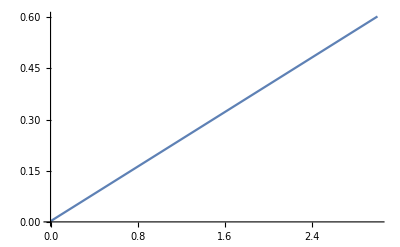

```mathematica
Plot[(0.01+s)/5,{s,0,3}]
```

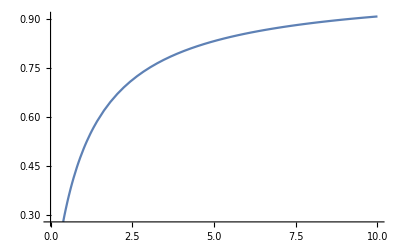

```mathematica
Plot[(s/(1+s)),{s,0,10}]
```

```mathematica
x:=((2 *0.5 * 0.01)/(1 *s- 0.5  + 1 *s*0.01 +0.5* 0.01 +√((0.01* s - 0.5  + 1* s* 0.01 + 0.5*  0.01)^2 -4(1 *s - 0.5) *0.5 *0.01) ))
```

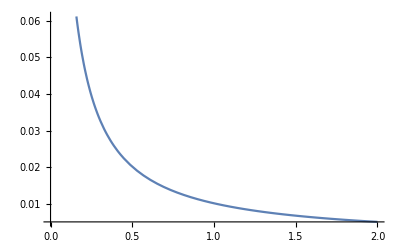

```mathematica
Plot[x,{s,0,2}]
```

```mathematica
y:=((2 *1*s * 0.05)/(0.4 - 1 *s + 0.4 *0.05 +1*s* 0.05 +√((0.4 - 1 *s + 0.4*0.05 + 1*s*  0.05)^2 -4(0.4  - 1*s) 1*s *0.05) ))
```

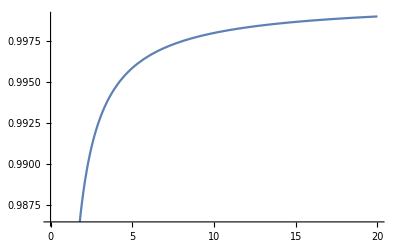

```mathematica
Plot[y,{s,0,20}]
```

```mathematica
prod101 := k0*((2 k3 r[t] j4)/(k4 - k3 r[t] + k4 j3 +k3 r[t] j4 +√((k4 - k3 r[t] + k4 j3 + k3 r[t] j4)^2 -4(k4 - k3 r[t]) k3 r[t] j4) )) +k1 s
```

```mathematica
reduc101 := k2 r[t] +k22 x[t] r[t]
```

```mathematica
part10 = {k0->4,k1 ->1,k2 -> 1,k22 ->1,k3 -> 1,k4 -> 1,k5 -> 0.1, j3 -> 0.3, j4 -> 0.3 }
```

{k0→4,k1→1,k2→1,k22→1,k3→1,k4→1,k5→0.1,j3→0.3,j4→0.3}

{k0→4,Null,k1→1,k2→1,k22→1,k3→1,k4→1,k5→0.1,j3→0.3,j4→0.3}

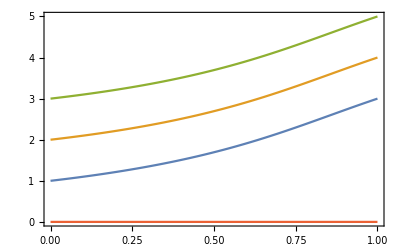

```mathematica
a9 = Plot[{(prod101/. part10)/. s->1,(prod101/. part10)/. s->2,(prod101/. part10) /. s->3, reduc101 /. part10/.x[t] ->1},{r[t],0,1},Frame->True]
```

Q.no. 7: Phase portrait and bifurcation diagram for the ‘activator-inhibitor device’

```mathematica
sol :=NDSolve[{r'[t]==((2*r[t]*0.3)/(1-r[t]+0.3+r[t]*0.3+√((1-r[t]+0.3+r[t]*0.3)^(2) -4(1-r[t])*r[t]*0.3)))+2-r[t]-x[t]*r[t],x'[t]==0.1*r[t]-0.075*x[t],x[0]==0,r[0]==0},{x,r},{t,0,10}]
```

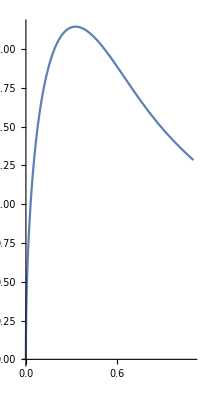

```mathematica
ParametricPlot[Evaluate[{x[t],r[t]}/.sol],{t,0,10}]
```